Analisi della Risposta libera, caso TC, per un sistema “planare” che presenta una coppia di autovalori complessi e coniugati

```mathematica
A={{-1/2,1/2},{-5/2,-3/2}}
```

{{-1/2,1/2},{-5/2,-3/2}}

```mathematica
C1={2,-1}
```

{2,-1}

Calcolo il polinomio caratteristico di A

```mathematica
CharacteristicPolynomial[A,x]
```

2+2 x+x^2

```mathematica
Simplify[A.A+2 A +2IdentityMatrix[2]]
```

{{0,0},{0,0}}

Calcolo gli autovalori di A

```mathematica
λ=Eigenvalues[A]
```

{-1+ⅈ,-1-ⅈ}

```mathematica
σ=Re[λ[[1]]]
```

-1

```mathematica
ω=Im[λ[[1]]]
```

1

Grafico dei modi naturali

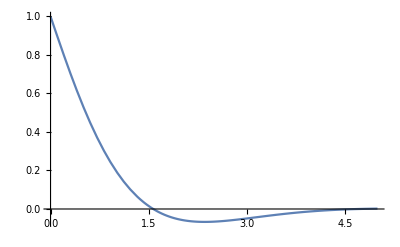

```mathematica
Plot[Exp[σ t]Cos[ω t],{t,0,5},PlotRange->All]
```

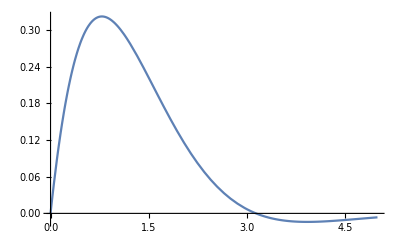

```mathematica
Plot[Exp[σ t]Sin[ω t],{t,0,5},PlotRange->All]
```

Calcolo la risposta libera a partire dalla matrice di cambiamento di base che genera la forma Rotation-Scaling Tempo Continuo

```mathematica
T=Simplify[Transpose[Eigenvectors[A]]]
```

{{-1/5-(2 ⅈ)/5,-1/5+(2 ⅈ)/5},{1,1}}

```mathematica
T//MatrixForm
```

(-1/5-(2 ⅈ)/5 | -1/5+(2 ⅈ)/5
1 | 1)

```mathematica
λ
```

{-1+ⅈ,-1-ⅈ}

```mathematica
T̂=Simplify[Transpose[{Re[T[[All,1]]],Im[T[[All,1]]]}]]
```

{{-1/5,-2/5},{1,0}}

```mathematica
T̂//MatrixForm
```

(-1/5 | -2/5
1 | 0)

```mathematica
T//MatrixForm
```

(-1/5-(2 ⅈ)/5 | -1/5+(2 ⅈ)/5
1 | 1)

```mathematica
Λ̂=Simplify[Inverse[T̂].A.T̂]
```

{{-1,1},{-1,-1}}

```mathematica
MatrixForm[Λ̂]
```

(-1 | 1
-1 | -1)

```mathematica
Subscript[x, 0]={{1},{0}}
```

{{1},{0}}

```mathematica
Subscript[z, 0]=Inverse[T̂].Subscript[x, 0]
```

{{0},{-5/2}}

```mathematica
x[t_]:=Simplify[T̂.({{Exp[σ t]Cos[ω t], Exp[σ t]Sin[ω t]}, {-Exp[σ t]Sin[ω t], Exp[σ t]Cos[ω t]}}).Subscript[z, 0]]
```

```mathematica
x[t]
```

{{1/2 ⅇ^-t (2 Cos[t]+Sin[t])},{-5/2 ⅇ^-t Sin[t]}}

```mathematica
y[t_]:=Simplify[C1.x[t]]
```

```mathematica
y[t]
```

{1/2 ⅇ^-t (4 Cos[t]+7 Sin[t])}

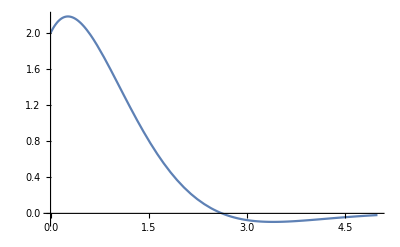

```mathematica
Plot[y[t],{t,0,5},PlotRange->All]
```